```mathematica
(*IMPOTAR DATOS*)
datos=Import["/Users/miguel/Desktop/Delfín/Mathematica/datos.txt","Table"];
datos // TableForm



vertices={{0,5000,1},{2500,5000,2},{4000,5000,3},{5000,5000,4},{0,3000,5},{2000,3000,6},{2500,3000,7},{4000,2750,8},{5000,2750,9},{2000,2000,10},{2500,2000,11},{3750,2000,12},{4000,2000,13},{5000,2000,14},{3750,1250,15},{5000,1250,16},{0,500,17},{2000,500,18},{0,0,19},{2000,0,20},{3750,0,21},{5000,0,22}};
aristas={{1,2,2500},{2,3,1500},{3,4,1000},{5,6,2000},{6,7,500},{8,9,1000},{10,11,500},{11,12,1250},{12,13,250},{13,14,1000},{15,16,1250},{17,18,2000},{19,20,2000},{20,21,1750},{21,22,1250},{4,9,2250},{9,14,750},{14,16,750},{16,22,1250},{3,8,2250},{8,13,750},{12,15,750},{15,21,1250},{2,7,2000},{7,11,1000},{6,10,1000},{10,18,1500},{18,20,500},{1,5,2000},{5,17,2500},{17,19,500}};
```

10 | 5000 | 5000 | 
2000 | 3000 | 2500 | 2000
4000 | 2750 | 5000 | 2000
0 | 5000 | 2500 | 3000
2500 | 5000 | 4000 | 2000
4000 | 5000 | 5000 | 2750
2000 | 2000 | 3750 | 0
3750 | 2000 | 5000 | 1250
3750 | 1250 | 5000 | 0
0 | 500 | 2000 | 0
0 | 3000 | 2000 | 500
7 |  |  |

Aristas No Dirigidas, Pesos de Aristas y Coordenadas de Vértices

```mathematica
nEdges=Map[#_⟦1⟧<->#_⟦2⟧&,aristas];
```

```mathematica
eWeigth=Map[#_⟦3⟧&,aristas];
```

```mathematica
coord=Map[Take[#,2]&,vertices];
```

Calculo de Cantidad de Aristas y Pesos de Aristas

```mathematica
Length[nEdges];
Length[eWeigth];
Length[coord];
```

Relación de Aristas con sus Pesos

```mathematica
eEdges=Map[nEdges_⟦#⟧->eWeigth_⟦#⟧&,Range[Length[nEdges]]];
```

Construcción del Gráfo a partir de las Aristas, Pesos y Coordenadas

```mathematica
g=Graph[nEdges,VertexLabels->"Name",VertexSize->Medium,EdgeWeight->eWeigth,VertexCoordinates->coord,EdgeLabels->eEdges];
```

Generacion de la lista de poligonos

```mathematica
obtenerListaPoligonos[grafo_,dat_]:=Module[{ g,listaDeVertices,coordenadas,poligonInd,vertice1,vertice2,vertice3,vertice4,coorx1,coorx2,coory1,coory2,
auxiliar,  datos , poligonos},
g=grafo;
datos=dat;
listaDeVertices = VertexList[g];
(*LISTA DE COORDENADAS DE LOS VERTICES DEL GRAFO*)
coordenadas=GraphEmbedding[g];
(*VARIABLES AUXILIARES*)
poligonos={};
vertice1 =0;
(*COORDENADAS DEL VERTICE SUPERIOR IZQUIERDO*)
coorx1=0;
coorx2 =0;
vertice2 =0;
(*COORDENADAS DEL VETICE INFERIOR DERECHO*)
coory1=0;
coory2=0;
vertice3 =0;
vertice4=0;
(*VARIABLE PARA CONSTRUIR EL POLIGONO*)
poligonInd={};
(*AUXILIAR DE VERTICE*)
auxiliar=0;

(*SE RECORREN LAS FILAS DEL ARCHIVO IMPORTADO SALTANDO LA FILA 1*)
For[i=2, i<Length[datos], i++,
(*LA VARIABLE DEL POLIGONO SE LIMPIA*)
poligonInd={};
(*SE DIVIDE EL PROCESO EN DOS, PARA CADA VERTICE EN LA FILA(CADA FILA TIENE 2 VERTICES)*)
For[j=1, j≤ 2, j++,
(*SI ES EL PRIMER CICLO, SE PROCESA EL PRIMER VERTICE*)
If[j==  1,
(*SE OBTIENE EL VERTICE DEL GRAFO QUE CORRESPONDA CON LAS COORDENADAS DADAS EN EL ARCHIVO IMPORTADO*)
vertice1 =Position[coordenadas,{datos[[i]][[1]],datos[[i]][[2]]}][[1]][[1]];
(*SE GUARDAN LAS COORDENADAS DEL VERTICE*)
coorx1 =datos[[i]][[1]];
coory1= datos[[i]][[2]];
,
(*SI ES EL SEGUNDO CICLO, SE PROCESA EL SEGUNDO VERTIDE DE LA FILA DEL ARCHIVO IMPORTADO*)
(*SE GUARDA EL VERTICE*)
vertice2=Position[coordenadas,{datos[[i]][[3]],datos[[i]][[4]]}][[1]][[1]];
(*SE GUARDAN LAS COORDENADAS DEL SEGUNDO EVRTICE*)
coorx2 = datos[[i]][[3]];
coory2= datos[[i]][[4]];
];

];
(*UNA VEZ SE TIENEN LOS VERTICES Y SUS RESPECTIVAS COORDENADAS...*)
(*SE CALCULAN LOS OTROS VERTICES DEL RECTANGULO CON LA MEZCLA DE LAS COORDENADAS DE LOS VERTICES ANTERIORES*)
vertice3 = Position[coordenadas,{coorx1,coory2}][[1]][[1]];
vertice4 = Position[coordenadas,{coorx2,coory1}][[1]][[1]];


(*SE PROCESA EL RECTANGULO PARA ENCONTRAR VERTICES INTERMEDIOS QUE FORMAN PARTE DEL POLIGONO*)
(*EL PROCESO SE REALIZA EN SENTIDO CONTRARIO A LAS MANECILLAS DEL RELOJ, INICIANDO CON EL VERTICE 1, SEGUIDO DEL 3, DEL 4 Y DEL 2*)
(*OBTENER LAS CONEXIONES INTERMEDIAS DE LA HORIZONTAL IZQUIERDA*)
auxiliar = vertice1;
(*SE RECORREN LAS COORDENADAS DE LOS VERTICES DEL GRAFO*)
For[k =1, k≤Length[coordenadas],k++,
(*SI HORIZONTALMENTE SE ENCUENTRA EN LA POSICION DEL PRIMER VERTICE, SE VERIFICA QUE ESTE ENTRE EL VERTICE 1 Y 3*)
If[coordenadas[[k]][[1]]==  coorx1 &&  coordenadas[[k]][[2]]< coory1 && coordenadas[[k]][[2]]>coory2,
(*SE CONECTA ESTE VERTICE CON EL ANTERIOR Y SE AGREGA A LA VARIABLE POLIGONO*)
AppendTo[poligonInd,auxiliar<->k ];
(*EL AUXILIAR SE CONVIERTE EN EL ULTIMO VERTICE*)
auxiliar = k;
]
];
(*SE CONECTA EL ULTIMO VERTICE CON EL VERTICE 3*)
AppendTo[poligonInd,auxiliar<->vertice3];



(*EL PROCESO ANTERIOR SE REPITE EN LOS LADOS RESTANTES*)
(*OBTENER LAS CONEXIONES INTERMEDIAS DE LA VERTICAL INFERIOR*)
auxiliar = vertice3;
For[k =1, k≤Length[coordenadas],k++,
If[coordenadas[[k]][[2]]==  coory2 &&  coordenadas[[k]][[1]]> coorx1 && coordenadas[[k]][[1]]<coorx2,
AppendTo[poligonInd,auxiliar<->k ];
auxiliar = k;
]
];
AppendTo[poligonInd,auxiliar<->vertice2];

(*OBTENER LAS CONEXIONES INTERMEDIAS DE LA HORIZONTAL DERECHA*)
auxiliar = vertice2;
For[k =1, k≤Length[coordenadas],k++,
If[coordenadas[[k]][[1]]==  coorx2 &&  coordenadas[[k]][[2]]< coory1 && coordenadas[[k]][[2]]>coory2,
AppendTo[poligonInd,auxiliar<->k ];
auxiliar = k;
]
];
AppendTo[poligonInd,auxiliar<->vertice4];

(*OBTENER LAS CONEXIONES INTERMEDIAS DE LA VERTICAL SUPERIOR*)
auxiliar = vertice4;
For[k =1, k≤Length[coordenadas],k++,
If[coordenadas[[k]][[2]]==  coory1 &&  coordenadas[[k]][[1]]> coorx1 && coordenadas[[k]][[1]]<coorx2,
AppendTo[poligonInd,auxiliar<->k ];
auxiliar = k;
]
];
AppendTo[poligonInd,auxiliar<->vertice1];
AppendTo[poligonos,poligonInd];
];
(*LA VARIABLE FINAL CONTIENE LA LISTA DE LOS POLIGONOS*)
poligonos

]
```

Obtencion de la lista de vertices en la periferia

```mathematica
getListOfPeriferia[v_]:= Module[{vertices,xs,ys,maxX,maxY,verticesPeriferia},
vertices=v;
(*COORDENADAS DE X*)
xs={};
(*COORDENADAS DE Y*)
ys={};
For[x=1,x≤Length[vertices],x++,
AppendTo[xs,vertices[[x]][[1]] ];
AppendTo[ys,vertices[[x]][[2]] ]
];

(*OBTENER LAS COORDENADAS MAYOYES DEL GRAFO; PARA CONOCER LOS LIMITES*)
(*OBTENCION DE LA COORDENADA EN X MAYOR*)
maxX = Max[xs];
(*OBTENCION DE LA COORDENADA EN Y MAYOR*)
maxY = Max[ys];

(*VARIABLE CONTENEDORA DE LOS VERTICES QUE SE ENCUENTREN EN LA PERIFERIA*)
verticesPeriferia= {};
(*SE RECORRE LA LISTA DE VERTICES Y SUS COORDENADAS*)
For[x=1, x≤Length[vertices],x++,
(*SI LA COORDENADA X O Y SE ENCUENTRA EN LOS LÍMITES DEL GRAFO, ES UN VERTICE EN LA PERIFERIA*)
If[vertices[[x]][[1]]== maxX || vertices[[x]][[2]]== maxY || vertices[[x]][[2]]== 0 || vertices[[x]][[1]]== 0 ,
(*SE AGREGA EL VERTICE A LA LISTA DE VERTICES EN LA PERIFERIA*)
AppendTo[verticesPeriferia, vertices[[x]][[3]] ]
];
];
(*VERTICES DE LA PERIFERIA*)
verticesPeriferia
]
```

Algoritmo para la obtencion de la ruta crítica

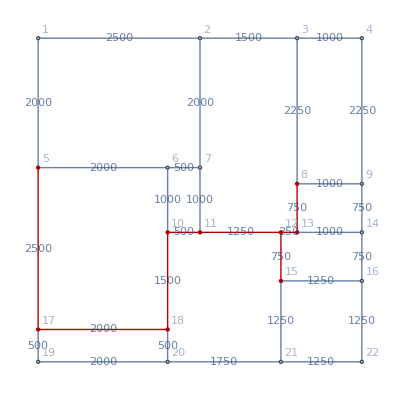

VERTICES COMPARTIDOS:

{5,18,10,8,12,15}

CAMINO ENTRE LOS VERTICES

{{5,17,18},{18,10},{10,11,12,13,8},{8,13,12},{12,15}}

SOLUCIÓN:

-Graphics-

```mathematica
(*OBTENER LA LISTA DE LOS POLIGONOS EN EL GRAFO*)
Poligonos=obtenerListaPoligonos(g,datos);
(*OBTENER LA LISTA DE LOS VERTICES DE LA PERIFERIA*)
verticesPeriferia = getListOfPeriferia[vertices];


(*OBTENER LOS VERTICES QUE COMPONEN A LOS POLIGONOS*)
verticesEnPoligonos ={};


For[x=1, x≤ Length[Poligonos], x++,
AppendTo[verticesEnPoligonos, VertexList[Poligonos[[x]]] ]
]
(*VARIABLE QUE CONTIENE LOS VERTICES DE CADA POLIGONO*)
verticesEnPoligonos;

(*VARIABLES BANDERAS PARA OBTENER EL VERTICE CON MAYORES CONEXIONES*)
vertice =0;
cantidadConexiones =0;
contador =0;
(*LISTA DE VERTICES COMPARTIDOS*)
verticesCompartidos = {};



(*SE SELECCIONA EL PRIMERO DE LOS POLIGONOS CUYO VERTICE ESTE EN LA PERIFERIA PARA ANALIZARLO*)
(*SE RECORRE LA LISTA DE POLIGONOS*)
For[i = 1, i≤ Length[verticesEnPoligonos],i++,
(*SE RECORREN LOS VERTICES DEL POLIGONO*)
For[j=0, j≤Length[verticesEnPoligonos[[i]]],j++,
If[MemberQ[verticesPeriferia,verticesEnPoligonos[[i]][[j]] ],
(*SI EL VERTICE ES DE LA PERIFERIA SE SELEECIONA Y SE SALE DEL CICLO*)
poligonoSeleccionado = verticesEnPoligonos[[i]];
Break[]
]
]
]
(*SE OBTIENE LA LISTA DE LOS POLIGONOS COMO AUXILIAR*)
listaDePoligonos = verticesEnPoligonos;



(*OBTENER EL VERTICE CON MAYORES CONEXIONES*)
For[x=1, x≤Length[poligonoSeleccionado], x++,
(*SE VERIFICA QUE SEA UN VERTICE DE LA PERIFERIA*)
If[MemberQ[verticesPeriferia,poligonoSeleccionado[[x]]],
contador =0;
(*SE CUENTA CON CUANTOS VERTICES TIENE CONEXION*)
For[i=1, i≤ Length[verticesEnPoligonos],i++,
If[MemberQ[verticesEnPoligonos[[i]],poligonoSeleccionado[[x]]  ],
contador= contador +1;
];
(*SI LA CANTIDAD DE CONEXIONES ES MAYOR A LA BANDERA, SE REMPLAZAN LOS VALORES DE LAS BANDERAS*)
If[contador>cantidadConexiones,
cantidadConexiones = contador;
vertice = poligonoSeleccionado[[x]];
]
]
]
]
AppendTo[verticesCompartidos,vertice];

g
(*ELIMINAR LOS POLIGONOS QUE COMPARTEN EL VERTICE*)
For[i=1, i≤ Length[listaDePoligonos],i++,
If[MemberQ[listaDePoligonos[[i]],vertice],
listaDePoligonos=Delete[listaDePoligonos,i];
i = i-1;
]
]

(*CICLO*)
While[Length[listaDePoligonos]!=0,
(*OBTENER EL VERTICE CON MÁS CONEXIONES*)
vertice =0;
cantidadConexiones =0;
(*SE CUENTA CON CUANTOS VERTICES TIENE CONEXION*)
For[x=1, x≤Length[poligonoSeleccionado], x++,
contador =0;
(*SE CUENTA CON CUANTOS VERTICES TIENE CONEXION*)
For[i=1, i≤ Length[listaDePoligonos],i++,
If[MemberQ[listaDePoligonos[[i]],poligonoSeleccionado[[x]]  ],
contador= contador +1;
];
(*SI LA CANTIDAD DE CONEXIONES ES MAYOR A LA BANDERA, SE REMPLAZAN LOS VALORES DE LAS BANDERAS*)
If[contador>cantidadConexiones,
cantidadConexiones = contador;
vertice = poligonoSeleccionado[[x]];
]
];
];
(*Print["vertice seleccionado".vertice];
Print["conexiones: ".cantidadConexiones];*)
(*SI EL POLIGONO YA NO COMPARTE CONEXION CON NINGUNO EN LA LISTA*)
If[contador == 0,
(*RECORRER LOS POLIGONOS*)
For[i=1, i≤Length[listaDePoligonos],i++,
(*RECORRER LOS VERTICES DE LOS POLIGONOS*)
For[j=1, j≤Length[listaDePoligonos[[i]]],j++,
(*UNA VEZ SE TIENE EL VERTICE, SE COMPARA CON TODOS LOS POLIGONOS*)
contador = 0;
For[k=1, k≤Length[verticesEnPoligonos],k++,
(*RECORRER LOS VERTICES DE LOS POLIGONOS*)
If[listaDePoligonos[[i]]≠ verticesEnPoligonos[[k]],
(*SI EL VERTICE TIENE CONEXION CON ALGUN OTRO POLIGONO*)
If[MemberQ[verticesEnPoligonos[[k]],listaDePoligonos[[i]][[j]]  ],
contador= contador +1;
];
];
(*SI LA CANTIDAD DE CONEXIONES ES MAYOR A LA BANDERA, SE REMPLAZAN LOS VALORES DE LAS BANDERAS*)
If[contador>cantidadConexiones,
cantidadConexiones = contador;
vertice = listaDePoligonos[[i]][[j]];
];

];
(*If[contador==0,
Print["Contador = 0".listaDePoligonos];
Print["Conexiones".cantidadConexiones];
Print["vErticesEnPoligonos".verticesEnPoligonos];
(*Abort[];*)
]*)

]
];
(*Print["verticeSeelccionado".vertice];
Print["conexiones".cantidadConexiones];*)
];
AppendTo[verticesCompartidos,vertice];
(*ELIMINAR LOS POLIGONOS QUE CONTIENEN EL VERTICE SELECCINADO*)
For[i=1, i≤ Length[listaDePoligonos],i++,
If[MemberQ[listaDePoligonos[[i]],vertice],
listaDePoligonos=Delete[listaDePoligonos,i];
i = i-1;
];
];
(*Print["lista de poligonos".listaDePoligonos];*)
 ]
(*LISTA DE VERTICES COMPARTIDOS FINAL*)
Print["VERTICES COMPARTIDOS:"]
verticesCompartidos
(*VARIABLE QUE CONTENDRÁ LAS RUTAS CORTAS*)
caminocorto={};
(*RECORRER LA LISTA DE LOS VERTICES PARA ENCONTRAR LA RUTA CORTA ENTRE ELLOS*)
For[i=1, i<Length[verticesCompartidos],i++,
(*AGREGAR LAS RUTAS A LA VARIABLE DE CAMINO MAS CORTO*)
AppendTo[caminocorto,FindShortestPath[g,verticesCompartidos[[i]],verticesCompartidos[[i+1]]]];
(*HIGLIGHT LA RUTA HECHA EN EL GRAFO*)
g=HighlightGraph[g,PathGraph[caminocorto[[i]]]];
]
(*IMPRIMIR EL CAMINO MÁS CORTO ENTRE LOS VERTICES SELECCIONADOS*)
Print["CAMINO ENTRE LOS VERTICES"]
caminocorto
(*MOSTRAR EL GRAFO Y EL CAMINO ENCONTRADO*)
Print["SOLUCIÓN:"]
g
```